```mathematica
ρ:=1200
m:=10
l:=Sqrt[1]
n:=ρ*l^2
"possible ploting points" n^2
A=CSMinkowski2Diamond[l,n];
Subscript[C, 1]=CausalMatrix[A];
Subscript[T, 1]=DistanceMatrixC[A,All,"Timelike"];
T=Subscript[T, 1]*Subscript[C, 1];
K=1/2 Subscript[C, 1].Inverse[IdentityMatrix[n]+m^2/(2ρ)Subscript[C, 1]];
points:=Transpose[{Flatten[T],Flatten[K]}];
```

1440000 possible ploting points

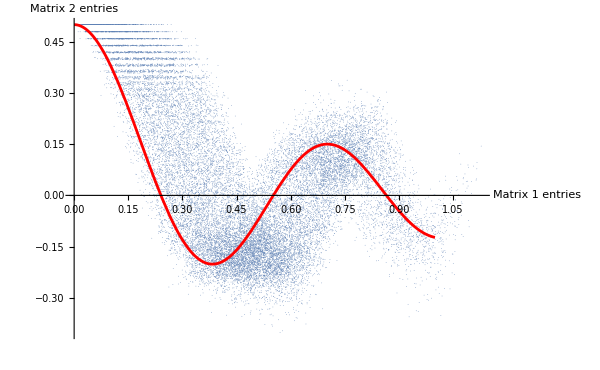

```mathematica
sample:=100000
(*ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Matrix 1 entries","Matrix 2 entries"}]
Plot[1/2 BesselJ[0,m*x],{x,0,l}]
*)
Subscript[plot, 1]=ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Matrix 1 entries","Matrix 2 entries"}];
Subscript[plot, 2]=Plot[1/2 BesselJ[0,m*x],{x,0,l},PlotStyle->Red];
Show[Subscript[plot, 1],Subscript[plot, 2]]
```